## Analytical solution :

```mathematica
Remove[θ,ω,g,l]
m1=I*(-ω*Sin[θ]+√(ω^2*(Sin[θ])^2+g/l))
m2=I*(-ω*Sin[θ]-√(ω^2*(Sin[θ])^2+g/l))
m={{1,1},{m1,m2}}
m.{x,y}=={0,1+I}
Solve[%,{x,y}]
```

ⅈ (-ω Sin[θ]+√(g/l+ω^2 Sin[θ]^2))

ⅈ (-ω Sin[θ]-√(g/l+ω^2 Sin[θ]^2))

{{1,1},{ⅈ (-ω Sin[θ]+√(g/l+ω^2 Sin[θ]^2)),ⅈ (-ω Sin[θ]-√(g/l+ω^2 Sin[θ]^2))}}

{x+y,ⅈ y (-ω Sin[θ]-√(g/l+ω^2 Sin[θ]^2))+ⅈ x (-ω Sin[θ]+√(g/l+ω^2 Sin[θ]^2))}=={0,1+ⅈ}

{{x→(1/2-ⅈ/2)/(√((g+l ω^2 Sin[θ]^2)/l)),y→-(1/2-ⅈ/2)/(√((g+l ω^2 Sin[θ]^2)/l))}}

```mathematica
Matching results of Analytical solution with numerical solution  Using plots:::
```

```mathematica
θ=Pi/4
ω=7.3*10^-5
l=100
g=10
m1=I*(-ω*Sin[θ]+√(ω^2*(Sin[θ])^2+g/l))
m2=I*(-ω*Sin[θ]-√(ω^2*(Sin[θ])^2+g/l))
m={{1,1},{m1,m2}}
m.{x,y}=={0,1+I}
Solve[%,{x,y}]
```

π/4

0.000073

100

10

0.+0.316176 ⅈ

0.-0.316279 ⅈ

{{1,1},{0.+0.316176 ⅈ,0.-0.316279 ⅈ}}

{x+y,(0.+0.316176 ⅈ) x-(0.+0.316279 ⅈ) y}=={0,1+ⅈ}

{{x→1.58114-1.58114 ⅈ,y→-1.58114+1.58114 ⅈ}}

(1.58114-1.58114 ⅈ) ⅇ^((0.+0.316176 ⅈ) t)-(1.58114-1.58114 ⅈ) ⅇ^((0.-0.316279 ⅈ) t)

1/2 ((1.58114-1.58114 ⅈ) ⅇ^((0.+0.316176 ⅈ) t)-(1.58114-1.58114 ⅈ) ⅇ^((0.-0.316279 ⅈ) t)+(1.58114+1.58114 ⅈ) ⅇ^((0.-0.316176 ⅈ) Conjugate[t])-(1.58114+1.58114 ⅈ) ⅇ^((0.+0.316279 ⅈ) Conjugate[t]))

-1/2 ⅈ ((1.58114-1.58114 ⅈ) ⅇ^((0.+0.316176 ⅈ) t)-(1.58114-1.58114 ⅈ) ⅇ^((0.-0.316279 ⅈ) t)-(1.58114+1.58114 ⅈ) ⅇ^((0.-0.316176 ⅈ) Conjugate[t])+(1.58114+1.58114 ⅈ) ⅇ^((0.+0.316279 ⅈ) Conjugate[t]))

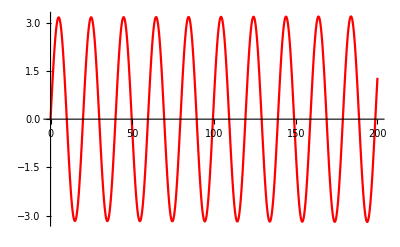

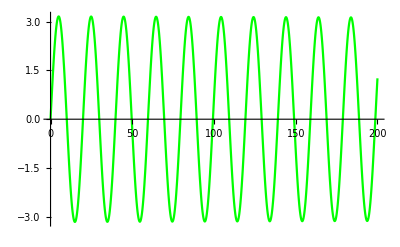

```mathematica
z=FullSimplify[(1.581138809019468-1.581138809019468 ⅈ)*Exp[m1*t]+(-1.581138809019468+1.581138809019468 ⅈ)*Exp[m2*t]]
x2=(z+Conjugate[z])/2
y2=(z-Conjugate[z])/(2*I)
Plot[x2,{t,0,200},PlotStyle->Red]
Plot[y2,{t,0,200},PlotStyle->Green]
```

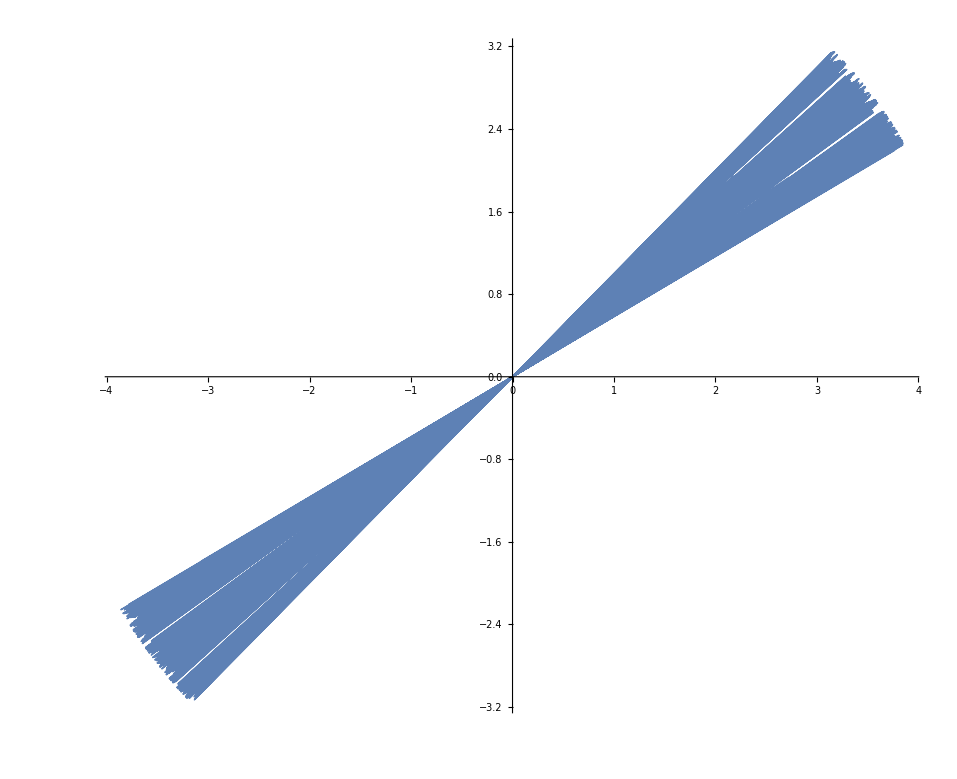

```mathematica
ParametricPlot[{x2,y2},{t,0,5000},PlotStyle->Thin]
```

Simplification of quantities x(t) and y(t):

```mathematica
FullSimplify[1/2 ((1.581138809019468-1.581138809019468 ⅈ) ⅇ^((0.+0.3161761514347557 ⅈ)t)-(1.581138809019468-1.581138809019468 ⅈ) ⅇ^((0.-0.31627938902480895 ⅈ)t)+(1.581138809019468+1.581138809019468 ⅈ) ⅇ^((0.-0.3161761514347557 ⅈ)t)-(1.581138809019468+1.581138809019468 ⅈ) ⅇ^((0.+0.31627938902480895 ⅈ)t))]
```

1.58114 Cos[0.316176 t]-1.58114 Cos[0.316279 t]+1.58114 Sin[0.316176 t]+1.58114 Sin[0.316279 t]

```mathematica
FullSimplify[-1/2 ⅈ ((1.581138809019468-1.581138809019468 ⅈ) ⅇ^((0.+0.3161761514347557 ⅈ) t)-(1.581138809019468-1.581138809019468 ⅈ) ⅇ^((0.-0.31627938902480895 ⅈ) t)-(1.581138809019468+1.581138809019468 ⅈ) ⅇ^((0.-0.3161761514347557 ⅈ)t)+(1.581138809019468+1.581138809019468 ⅈ) ⅇ^((0.+0.31627938902480895 ⅈ)t))]
```

-1.58114 Cos[0.316176 t]+1.58114 Cos[0.316279 t]+1.58114 Sin[0.316176 t]+1.58114 Sin[0.316279 t]